```mathematica
(* some auxiliary symbols *)
Q[k_]:={{Cos[α0+α],0,-Sin[α0+α]},{(-1)^k*Sin[α0+α],0,(-1)^k*Cos[α0+α]},{0,(-1)^(k+1),0}};
c[k_]:={Rm*Cos[α0+α],(-1)^k*Sin[α0+α],0}

xEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,1]])
yEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,2]])
zEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,3]])

X[k_,l_]:=xEigen[k]+(-1)^l*w
Y[k_,l_]:=yEigen[k]+(-1)^l*d
Z[k_]:=zEigen[k]

R[k_,l_,m_]:=Sqrt[X[k,l]^2+Y[k,m]^2+Z[k]^2]
```

```mathematica
(* potential *)
V=Sum[
(-1)^(k+l+m)*(
-Z[k]*ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]+X[k,l]*Log[Y[k,m]+R[k,l,m]]+Y[k,m]*Log[X[k,l]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
H=-Grad[V,{x,y,z}];
```

```mathematica
padx=2;
pady=2;

wVal=1/2;
dVal=1/2;

α0Val=0;
αVal=π/4;
RmVal=4;

pars={w->wVal,d->dVal,z->0,α0->α0Val, α->αVal,Rm->RmVal};
Hplot[x_,y_]=H/.pars;
```

```mathematica
padR=1;
canvas=Disk[{0,0},RmVal+padR];

magnetSegment=RegionDifference[Disk[{0,0},RmVal+wVal,{α0Val-αVal,α0Val+αVal}],
Disk[{0,0},RmVal-wVal,{α0Val-αVal,α0Val+αVal}]];
```

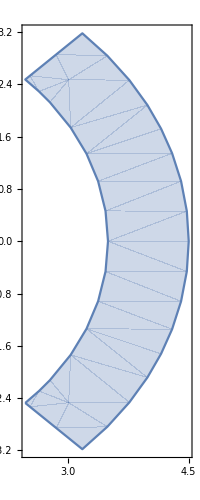

```mathematica
RegionPlot[magnetSegment,AspectRatio->Automatic]
```

```mathematica
Show[StreamDensityPlot[Hplot[x,y][[{1,2}]],{x,y}∈canvas],Graphics[magnetSegment]]
```

-Graphics-